```mathematica
SetOptions[Plot,BaseStyle-> {FontSize-> 12,FontFamily-> "Latin Modern Roman"},FrameStyle-> Black,ImageSize-> 350, AspectRatio-> 0.71,Frame-> True];

SetOptions[ListPlot,BaseStyle-> {FontSize-> 12,FontFamily-> "Latin Modern Roman"},FrameStyle-> Black,ImageSize-> 350, AspectRatio-> 0.71,Frame-> True];

Needs["MaTeX`"];

SetDirectory[NotebookDirectory[]];

DarkGreen=Darker[Green];
DarkBlue=Darker[Blue];
DarkRed=Darker[Red];
```

### Full event representation

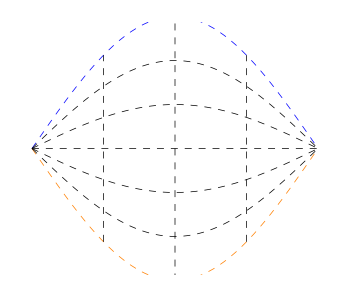

```mathematica
f[x_]:=Table[{x,y},{y,-π Sin[x],π Sin[x],2π Sin[x]/30}];
hor=ListLinePlot[{f[π/4],f[π/2],f[3 π/4]},PlotStyle->{{Black,Dashed, Thickness[0.0015]}}];
p1=Plot[{ π Sin[x],-π Sin[x], π/3 Sin[x],-π/3 Sin[x], 2 π/3 Sin[x],(-2π)/3 Sin[x],0},{x,0.0,π},PlotStyle->{{Blue,Dashed,Thickness[0.0015]},{Orange,Dashed,Thickness[0.0015]},{Black,Dashed,Thickness[0.0015]},{Black,Dashed,Thickness[0.0015]},{Black,Dashed,Thickness[0.0015]},{Black,Dashed,Thickness[0.0015]},{Black,Dashed,Thickness[0.0015]},{Black,Dashed,Thickness[0.0015]},{Black,Dashed,Thickness[0.0015]}}];
p1=Show[{p1,hor},Frame-> False,Axes-> False,AspectRatio->0.85,PlotRange-> {-0.92π,0.92π}]
```

```mathematica
textr=1.1;
labellist={
MaTeX[ "\\text{BF: anti-}k_T(ee)",Magnification->textr],
MaTeX[ "\\text{BF: anti-}k_T(pp)",Magnification->textr],
MaTeX[ "\\text{BF: Centauro}",Magnification->textr]
}
```

{-Graphics-,-Graphics-,-Graphics-}

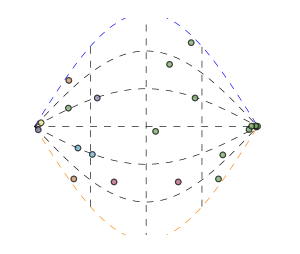

```mathematica
Table[data=Import["jet_"<>ToString[k-1]<>".txt","Table"];
points=ParallelTable[
e= data[[m,4]];
x=data[[m,3]];
y=data[[m,2]];
{x,y Sin[x] },{m,1,Length[data]}];
col=Mod[k,6]/6 +1/12;
Show[Table[ListPlot[{points[[i]]},PlotMarkers->{Graphics[{EdgeForm[Directive[Black,Thin]],Opacity[0.5],Disk[{0,0},1]}],0.05 data[[i,4]]^(1/3)},PlotStyle->ColorData["DarkBands"][col]],{i,1,Length[points]}]],
{k,1,10}];
Centauro=Show[p1,%,PlotRange->{{-0.1,3.35},{-0.92π,0.92π}},ImageSize-> 300]
```

```mathematica
Export["unfolded_sphere.pdf",%]
```

unfolded_sphere.pdf

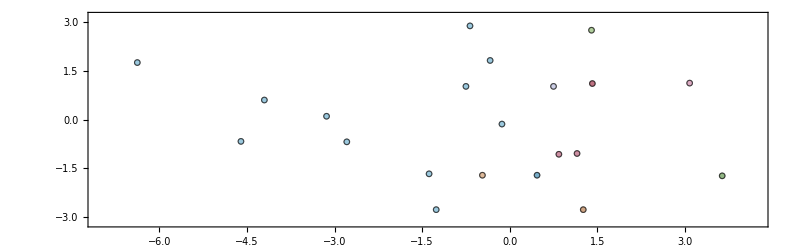

```mathematica
Table[data=Import["jet_"<>ToString[k-1]<>".txt","Table"];
points=ParallelTable[
e= data[[m,4]];
x=data[[m,1]];
y=data[[m,2]];
{x,y },{m,1,Length[data]}];
Show[Table[ListPlot[{points[[i]]},AspectRatio->0.31,
FrameLabel->(MaTeX[#,Magnification-> 4/3]&)/@{"\\eta","\\phi"},PlotMarkers->{Graphics[{EdgeForm[Directive[Black,Thin]],Opacity[0.5],Disk[{0,0},1]}],0.05 data[[i,4]]^(1/3)},PlotStyle->ColorData["DarkBands"][k/15]],{i,1,Length[points]}],PlotRange->{{-7.,4.2},{-1.01π,1.01 π}},ImageSize-> 800],
{k,1,10}];
ppboo=Show[{%}]
```

```mathematica
Export["eta_vs_phi.pdf",%]
```

eta_vs_phi.pdf

```mathematica
azimuthMAP[x_,y_]:=Piecewise[{{ArcTan[y/x], x  >0},{Sign[y] π/2-ArcTan[y/x], x<0}}]
```

```mathematica
eventU=Table[
data=Import["ungroomed_eCM@63_"<>ToString[k]<>"_HM.txt","Table"];
points=ParallelTable[
e= data[[i,1]];
x=data[[i,2]];
y=data[[i,3]];
z=data[[i,4]];
ϕ=azimuthMAP[x,y];
θ=ArcCos[z/√(x^2+y^2+z^2)] ;
{θ,ϕ Sin[θ] ,e},{i,1,Length[data]}];
Show[p1,
Table[
ListPlot[{points[[i,{1,2}]]},
Frame->True,
AspectRatio->1,
PlotMarkers->{Graphics[{EdgeForm[Directive[Black,Thin]],Opacity[0.1],Disk[{0,0},1]}],0.05 points[[i,3]]^0.2},
PlotStyle->Black],{i,1,Length[points]}],
PlotRange->{{-0.2,3.4},All},ImageSize-> 200 ] ,{k,1,12}];
```

```mathematica
eventGC=Table[
data=Import["groomedCentauro_eCM@63_"<>ToString[k]<>"_HM.txt","Table"];
points=ParallelTable[
e= data[[i,1]];
x=data[[i,2]];
y=data[[i,3]];
z=data[[i,4]];
ϕ=azimuthMAP[x,y];
θ=ArcCos[z/√(x^2+y^2+z^2)] ;
{θ,ϕ Sin[θ] ,e},{i,1,Length[data]}];
Show[p1,
Table[
ListPlot[{points[[i,{1,2}]]},
Frame->True,
AspectRatio->1,
PlotMarkers->{Graphics[{EdgeForm[Directive[Black,Thin]],Opacity[0.4],Disk[{0,0},1]}],0.05 points[[i,3]]^0.2},
PlotStyle->Darker[Green]],{i,1,Length[points]}],
PlotRange->{{0.,3.4},All},ImageSize-> 400 ] ,{k,1,12}];
```

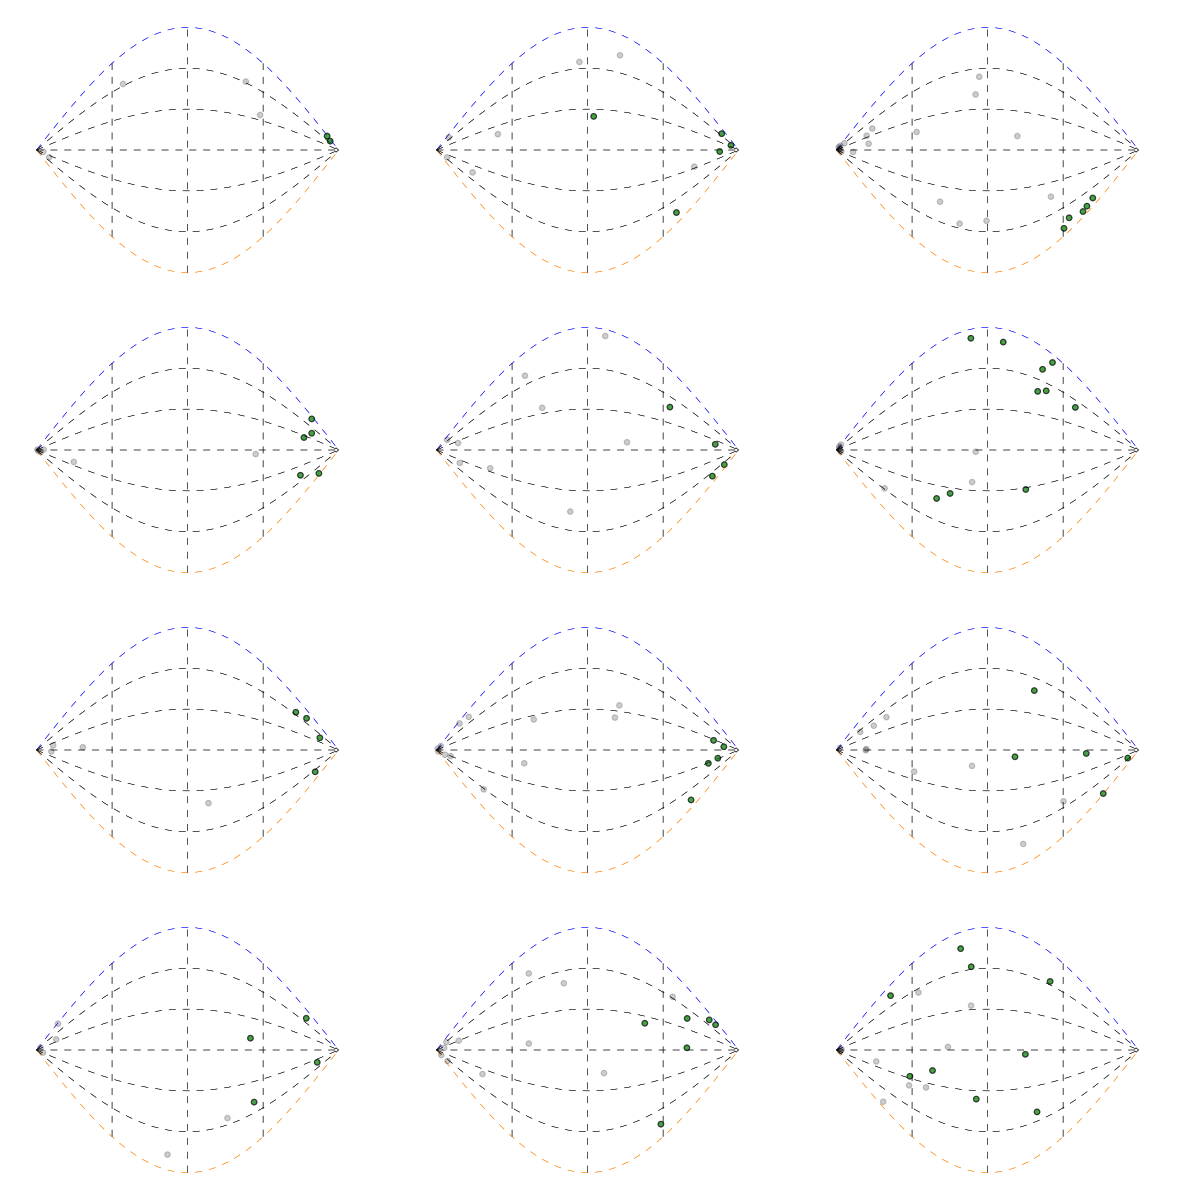

```mathematica
list=Table[Show[eventGC[[i]],eventU[[i]],ImageSize-> 200]  ,{i,1,12}];
Nrows=4;
sample=Grid[Table[list[[(i-1)Length[list]/Nrows +1;;i Length[list]/Nrows]],{i,1,Nrows}],Spacings->{0,0}]
```

```mathematica
Export["centauro_grooming.pdf",%]
```

centauro_grooming.pdf